## 2.5 Joint, Marginal, and Conditional Distributions

In this section we would like to take the ideas of conditional probability and independence that were introduced in Sections 1.5 and 1.6 into the domain of random variables and their distributions.  This transition should be a very straightforward one.  We already encountered the idea of joint distributions of random variables in Section 2.2 on the multinomial distribution, and we would like to explore this idea further, introduce the ideas of marginal and conditional distributions, and use those to define independence of random variables.
	Earlier we studied a contingency table for the Peotone airport problem, and a similar example here should motivate the ideas well.  Suppose that a researcher in cognitive psychology is conducting an experiment on memory.  She exposes to several subjects four numbers between 1 and 100 on flash cards, and after fifteen minutes she asks the subjects to recall the numbers.  The experimenter records how many of the numbers the subjects correctly recalled.  Then the same subjects are presented four more numbers between 1 and 100 orally.  After another fifteen minutes, the experimenter again records how many of them each subject got right.  At the end of the experiment, she classifies each subject as to how many of the numbers that were shown visually and how many that were spoken were correctly remembered.  Assume that the frequencies are in the table below.  I have computed the total number of subjects in each row and column for your convenience.

| Y = visual correct | 0 | 1 | 2 | 3 | 4 | row sum
  | 0 | 4 | 6 | 10 | 8 | 3 | 31
X = oral | 1 | 2 | 5 | 7 | 12 | 6 | 32
correct | 2 | 1 | 4 | 10 | 15 | 6 | 36
  | 3 | 2 | 6 | 9 | 14 | 10 | 41
  | 4 | 1 | 3 | 5 | 11 | 11 | 31
  | col sum | 10 | 24 | 41 | 60 | 36 | 171

Consider the experiment of picking a subject randomly from this group of 171 subjects.  Let X and Y, respectively, denote the oral and visual scores of the subject.  Then, for instance,

P[X=0, Y=0] = 4/171, P[X=0, Y=1] = 6/171, P[X=0, Y=2] = 10/171,

etc.  The complete list of the probabilities

f(x,y) = P[X=x, Y=y]

over all possible values (x, y) is called the joint probability mass function of the random variables X and Y.  Joint mass functions for more than two discrete random variables are defined similarly (see Exercise 14).

Activity 1.   Referring to the memory experiment, what is P[X = 0]? P[X = 1]? P[X = 2]? P[X = 3]? P[X = 4]?  What do these probabilities add to?

The activity above suggests another kind of distribution that is embedded in the joint distribution described by f.  Working now with Y using the column sums we find:

P[Y=0] = 10/171; P[Y=1] = 24/171; P[Y=2] = 41/171; P[Y=3] = 60/171; P[Y=4] = 36/171

It is easy to check that these probabilities sum to 1; hence, the function q(y)=P[Y=y] formed in this way is a valid probability mass function. Notice that to compute each of these probabilities, we add up joint probabilities over all x values for the fixed y of interest, for example,

P[Y = 0]  | = | P[X = 0, Y = 0] + P[X = 1, Y = 0] + P[X = 2, Y = 0]
  |   | + P[X = 3, Y = 0] + P[X = 4, Y = 0]
  | = | 4/171 + 2/171+ 1/171 + 2/171 + 1/171
  | = | 10/171

The Law of Total Probability justifies this procedure.

In general, the marginal probability mass function of Y is

q(y)=P[Y=y]=∑_x P[X=x,Y=y]=∑_x f(x,y)

where f is the joint p.m.f. of X and Y.  Similarly, the marginal probability mass function of X is obtained by adding the joint p.m.f. over all values of y:

p(x)=P[X=x]=∑_y P[X=x,Y=y]=∑_y f(x,y)

The idea of a conditional distribution of one discrete random variable given another is analogous to the discrete conditional probability of one event given another.  Using the memory experiment again as our model, what is the conditional probability that a subject gets 2 visual numbers correct given that the subject got 3 oral numbers correct?  The condition on oral numbers restricts the sample space to subjects in the line numbered 3 in the table, which has 41 subjects.  Among them, 9 got 2 visual numbers correct.  Hence,

P[Y=2 | X=3] = 9/41

It should be easy to see from this example that for jointly distributed discrete random variables, P[Y = y | X = x] is a well defined conditional probability of one event given another.  This leads us to the definition of the conditional probability mass function of Y given X = x:

q(y | x) = P[Y=y | X=x] = P[X=x, Y=y]/P[X=x] = (f(x,y))/(p(x))

Reasoning as above, the full conditional p.m.f. of Y given X=3 in the memory experiment is

P[Y=0 | X=3] = 2/41,P[Y=1 | X=3] = 6/41,P[Y=2 | X=3] = 9/41,P[Y=3 | X=3] = 14/41, P[Y=4 | X=3] = 10/41

Similarly, the conditional probability mass function of X given Y = y is

p(x | y) = P[X=x | Y=y] = P[X=x, Y=y]/P[Y=y] = (f(x,y))/(q(y))

Formulas (4) and (5) tie together the three kinds of distributions: joint, marginal, and conditional. The conditional mass function is the quotient of the joint mass function and the marginal mass function of the random variable being conditioned on.
	The concept of independence also carries over readily to two or more discrete random variables.  In the case of two discrete random variables X and Y, we say that they are independent of each other if and only if for all subsets A and B of their respective state spaces,

P[X∈A,Y∈B] = P[X∈A]·P[Y∈B]

(Exercise 15 gives the analogous definition of independence of more than two random variables.) Alternatively, we could define independence by the condition

P[Y∈B | X∈A] = P[Y∈B]

for all such sets A and B, with the added proviso that P[X ∈ A] ≠ 0.  (How does (7) imply the factorization criterion (6), and how is it implied by (6)?)
	 For example, from the memory experiment table, P[Y = 4 | X = 4] = 11/31, since there are 31 subjects such that X = 4, and 11 of them remembered 4 numbers that were visually presented. However, P[Y = 4] is only 36/171, so that the chance that 4 visual numbers are remembered is increased by the occurrence of the event that 4 auditory numbers were remembered. Even this one violation of condition (7) is enough to show that the random variables X and Y are dependent (that is, not independent). But in general, do you really have to check all possible subsets A of the X state space (2^5 = 32 of them here) with all possible subsets B of the Y state space (again 32 of them) in order to verify independence?  Fortunately the answer is no, as the following important activity shows.

Activity 2  Show that X and Y are independent if and only if their joint p.m.f. f(x,y) factors into the product of the marginal p.m.f.'s p(x)·q(y).

Thus, in our example instead of checking 32·32 = 1024 possible combinations of sets A and B, we need only check the factorization of f for 5·5 = 25 possible combinations of states x and y.  
	Independence for more than two random variables is explored in the exercises.  The basic idea is that several random variables are independent if and only if any subcollection of them satisfies factorization of intersection probabilities as in formula (6). This also follows if and only if the joint p.m.f. factors into the product of the marginals. 
	We will now look at a series of examples to elaborate on the ideas of joint, marginal, and conditional distributions and independence.

Example 1  In a roll of two fair 12-sided dice, let X and Y be the observed faces. What is the joint distribution of X and Y? Find a general formula for P[X+Y=z], z=2,3,… ,24. 
	We assume that X and Y are independent random variables, each with marginal p.m.f. f(x)=1/12, x=1,2,… ,12. By the result of Activity 2, the joint p.m.f. of these two random variables is the product of their marginals:

f(x,y) = p(x)·q(y) = 1/12·1/12=1/144, x,y =1,2,…,12

Now let Z = X + Y be the total of the two observed faces. In order for Z to equal z, X must assume one of its possible values x, and Y must equal z-x.  Then the distribution of Z is, by the law of total probability,

g(z) = P[Z=z] | = | Σ_(x=1)^(z-1) P[X=x,Y=z-x]

We need to consider separately the cases where z≤12 and z>12, because when z≤12 each joint probability in the sum above is non-zero, but when z>12 only terms such that both x and z-x are in {1,2,... ,12} are non-zero.  In the case z≤12,

g(z) = P[Z = z] | = | Σ_(x=1)^(z-1) P[X=x,Y=z-x]
  | = | Σ_(x=1)^(z-1) 1/144
  | = | 1/144(z-1), z=2,3,…,12

When z>12, we need both 1≤x≤12 and 1≤z-x≤12⟹x≥z-12.  Therefore,

g(z) = P[Z = z] | = | Σ_(x=z-12)^12 P[X=x,Y=z-x]
  | = | Σ_(x=z-12)^12 1/144
  | = | 1/144(12-(z-12)+1)
  | = | 1/144(25-z), z=13,14,…,24

You should convince yourself that this is an appropriate generalization of the distribution of the sum of the faces of two ordinary 6-sided dice. ■

Activity 3  In the previous example, find the conditional mass function of the sum Z given that X=x for each of the x values 2, 6, and 12.

Example 2  This example concerns a generalization of the hypergeometric distribution that we studied earlier.  Suppose that the faculty at Old VineCovered College is sharply divided along political lines, with 45 of the 100 faculty members who are political liberals, 30 who are centrists, and 25 who are political conservatives.  The Dean of the College is appointing a committee to revise the general education curriculum by selecting 8 faculty members at random, in a batch and without replacement, from the 100.  Let us find the joint distribution of the numbers of liberals, centrists, and conservatives on the committee, the marginal distributions of each political group, and the probability that the liberals will have a majority.
	In order to have, say i liberals, j centrists, and k conservatives on the committee, where i + j + k is required to be 8, we must select i liberals in a batch without replacement from the 45 liberals, and similarly j centrists from the 30 and k conservatives from the 25.  By combinatorics, since there are (100
8) possible equally likely committees,

f(i,j,k) | = | P[i liberals, j centrists, k conservatives]
  | = | (( 45 
i)( 30 
j)( 25 
k))/( 100 
8) , i,j,k ∈{0, 1, ... , 8}, i+j+k=8

Now the marginals may be found by using the definition in (2) of marginal p.m.f.'s and summing out over the other random variable states.  Try this in the activity that follows this example.  But we can also work by combinatorial reasoning.  In order to have exactly i liberals, we must select them from the subgroup of 45, and then select any other 8 - i people from the 55 non-liberals to fill out the rest of the committee.  Therefore, the marginal p.m.f. of the number of liberals on the committee is

p(i) = P[i liberals] = (( 45 
i)(  55 
8-i ))/( 100 
8)

Similarly, the other marginals are

q(j) = P[j centrists] = (( 30 
j)(  70 
8-j ))/( 100 
8),     r(k) = P[k conservatives] = (( 25 
k)(  75 
8-k ))/( 100 
8)

All of these marginal distributions are of the hypergeometric family.
	By the way, it is easy to check that

f(i,j,k) ≠ p(i)·q(j)·r(k)

so that the numbers of the three political types in the sample are not independent random variables.  Intuitively, knowing the number of liberals, for instance, changes the distribution of the number of centrists (see also Exercise 5).
	Now the probability that the liberals will have a majority is the probability that there are at least five liberals on the committee.  It is easiest to use the marginal distribution in formula (8) for the number of liberals, and then to let Mathematica do the computation:

P[liberals have majority] = ∑_(i=5)^8 (( 45 
i)(  55 
8-i ))/( 100 
8)

```mathematica
N[1-CDF[HypergeometricDistribution[8,45,100],4]]
```

0.251815

We see that the probability of a liberal majority occurring by chance is only about 1/4.  ■

Activity 4  In the above example, find p(i), the marginal p.m.f. of the number of liberals by setting k=8-i-j in the joint p.m.f. and then adding the joint probabilities over the possible j values.

Example 3  If two random variables X and Y are independent and we observe instances of them (X_1, Y_1), (X_2, Y_2), ... , (X_n, Y_n), what patterns would we expect to find?  
	We will answer the question by simulating the list of n pairs.  For concreteness, let X have the discrete p.m.f. p(1) = 1/4, p(2) = 1/4, p(3) = 1/2 and let Y have the discrete p.m.f. q(1) = 5/16, q(2) = 5/16, q(3) = 3/8.  The program below simulates two numbers at a time from Mathematica's random number generator and converts them to observations of X and Y, respectively.  If the random number generator works as advertised, the values of X and Y that are simulated should be (or appear to be) independent.  We will then tabulate the number of times the pairs fell into each of the 9 categories (1,1),(1,2),(1,3),(2,1),(2,2),(2,3),(3,1),(3,2),(3,3)  and study the pattern. 
	The first two commands simulate individual observations from the distributions described in the last paragraph, the third uses them to simulate a list of pairs, and the last tabulates frequencies of the nine states and presents them in a table.

```mathematica
SimX[]:=Module[{rand},rand=RandomReal[];If[rand<1/4,1,If[1/4≤rand<1/2,2,3]]]
```

```mathematica
SimY[]:=Module[{rand},rand=RandomReal[];If[rand<5/16,1,If[5/16≤rand<10/16,2,3]]]
```

```mathematica
SimXYPairs[numpairs_]:=Table[{SimX[],SimY[]},{numpairs}]
```

```mathematica
XYPairFrequencies[numpairs_]:=
	Module[{simlist,freqtable,nextpair,x,y},
		simlist=SimXYPairs[numpairs]; (* generate data *)
		freqtable=Table[0,{i,1,3},{j,1,3}]; (* initialize table *)
	  Do[nextpair=simlist[[i]]; (* set up next x,y pair *)
			    x=nextpair[[1]]; y = nextpair[[2]];
			    freqtable[[x,y]]=freqtable[[x,y]]+1,  (* increment the frequency table *)
			{i,1,Length[simlist]}];
		(* output the table *)
		TableForm[{{" ", "Y=1","Y=2","Y=3"},
			                      {"X=1",freqtable[[1,1]],freqtable[[1,2]],freqtable[[1,3]]},
		{"X=2",freqtable[[2,1]],freqtable[[2,2]],freqtable[[2,3]]},
				{"X=3",freqtable[[3,1]],freqtable[[3,2]],freqtable[[3,3]]}}]]
```

Below is a sample run.  There is some variability in category frequencies, even when the sample size is 1000, but a few patterns do emerge.  In each X row, the Y = 1 and Y = 2 frequencies are about equal, and the Y = 3 frequency is a bit higher.  Similarly, in each Y column, the X = 1 frequency is close to that of X = 2, and their frequencies are only around half that of X = 3. If you look back at the probabilities assigned to each state, you can see why you should have expected this. In general, if independence holds, the distribution of data into columns should not be affected by which row you are in, and the distribution of data into rows should not be affected by which column you are in. ■

```mathematica
SeedRandom[165481];
XYPairFrequencies[1000]
```

| Y=1 | Y=2 | Y=3
X=1 | 83 | 78 | 85
X=2 | 85 | 73 | 88
X=3 | 162 | 152 | 194

Activity 5  What characteristics of simulated contingency tables like the one in the last example would you expect in the case where the random variables are not independent?

Example 4  Suppose that a project is composed of two tasks that must be done one after the other, and the task completion times are random variables X and Y.  The p.m.f. of X is discrete uniform on the set {3,4,5}, and the conditional probability mass functions for Y given each of the three possible values for X are as in the table below. Find the probability distribution of the total completion time for the project, and find the probability that the project will be finished within 6 time units.

| Y=1 | Y=2 | Y=3
X=3 | 1/2 | 1/4 | 1/4
X=4 | 1/3 | 1/3 | 1/3
X=5 | 1/4 | 1/4 | 1/2

The possible values of the project completion time X+Y are {4,5,6,7,8}.  Itemizing cases and using the multiplication rule for conditional probability, we get:

P[X+Y=4]=P[X=3,Y=1]=P[Y=1|X=3]P[X=3]=1/2·1/3=1/6 =6/36,P[X+Y=5]=P[X=3,Y=2]+P[X=4,Y=1]=1/4·1/3+1/3·1/3=7/36 ,P[X+Y=6]=P[X=3,Y=3]+P[X=4,Y=2]+P[X=5,Y=1]=1/4·1/3+1/3·1/3+1/4·1/3=10/36 ,P[X+Y=7]=P[X=4,Y=3]+P[X=5,Y=2]=1/3·1/3+1/4·1/3=7/36 ,
P[X+Y=8]=P[X=5,Y=3]=1/2·1/3=1/6 =6/36

The probability that the completion time is less than or equal to 6 is the total of the first three of these, that is, 6/36+7/36+10/36=23/36. ■

### Exercises 2.5

1.  In the memory experiment example at the beginning of the section, find the conditional p.m.f. of Y given X = 0, and the conditional p.m.f. of X given Y = 2.

2.  Suppose that X and Y have the joint distribution in the table below.  Find the marginal distributions of X and Y.  Are X and Y independent random variables?

|   |   | Y |   |  
  |   | 1 | 2 | 3 | 4
  | 1 | 1/16 | 1/16 | 1/16 | 1/16
X | 2 | 1/32 | 1/32 | 1/16 | 1/16
  | 3 | 1/16 | 1/16 | 1/32 | 1/32
  | 4 | 1/8 | 1/8 | 1/16 | 1/16

3.  Argue that two discrete random variables X and Y cannot be independent unless their joint state space is a Cartesian product of their marginal state spaces, i.e., E = E_x × E_y = {(x,y): x ∈ E_x, y ∈ E_y}.

4.  Suppose that a joint p.m.f. f(x,y) puts equal weight on all the integer grid points marked in the diagram below.  Find:  (a) the marginal distribution of X;   (b) the marginal distribution of Y;  (c) the conditional distribution of X given Y = 1;  (d) the conditional distribution of Y given X = 1.

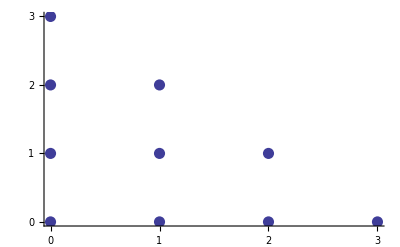

```mathematica
ListPlot[{{0,0},{1,0},{2,0},{3,0},{0,1},{1,1},{2,1},{0,2},{1,2},{0,3}},PlotStyle->PointSize[0.02],Ticks->{{0,1,2,3},{0,1,2,3}}]
```

Exercise 4

5.  In Example 2, find the conditional distribution of the number of centrists on the committee given that the number of liberals is 3.

6.  Show that if two discrete random variables X and Y are independent, then their joint cumulative distribution function, defined by F(x,y) = P[X ≤ x, Y ≤ y], factors into the product of the marginal c.d.f.'s F_x(x) = P[X ≤ x] and F_y(y) = P[Y ≤ y].

7.  In the contingency table below, subjects were classified according to their age group and their opinion about what should be done with a government budget surplus. One subject is drawn at random; let X denote the age category and let Y denote the opinion category for this subject.

(a) Compute the marginal distribution of X;

(b) Compute the marginal distribution of Y;

(c) Compute the conditional distribution of Y given that X is the 21-35 age category;

(d) Compute the conditional distribution of X given that Y is the Lower Taxes opinion category;

(e) Considering the data in the table to be a random sample of American voters, do the age group and opinion variables seem independent?

| Save Social  | Reduce National | Lower | Increase Defense
  | Security | Debt | Taxes | Spending
21-35 | 22 | 10 | 63 | 15
36-50 | 46 | 20 | 85 | 60
50-65 | 89 | 54 | 70 | 41
over 65 | 106 | 32 | 15 | 20

8.  (Mathematica)  Write a Mathematica program to simulate observations (X, Y) having the joint density in Exercise 4.

9.  Show that if two discrete random variables X and Y are independent under the intersection form of the definition, then for all x such that p(x) ≠ 0, q(y | x) = q(y), and for all y such that q(y) ≠ 0, p(x | y) = p(x), where p(x) and q(y) are the marginal p.m.f.'s of X and Y, and p(x|y) and q(y|x) are the conditional p.m.f.'s.

10.  Suppose that in baseball a pitcher throws a fastball (coded by 0), a curve (1), or a slider (2) with probabilities 1/2, 1/4, and 1/4, respectively.  Meanwhile the hitter guesses fastball (coded by 0 again), curve (1), or slider (2) with probabilities 5/8, 1/8, and 1/4, respectively. The hitter's guess is independent of the pitcher's choice.  The probabilities that the hitter will hit safely under each possible pair of pitcher pitches and hitter guesses are in the table below.  Find the probability that the hitter hits safely.

|   |   | Y |  
  |   |   | (hitter) |  
  |   | 0 | 1 | 2
  | 0 | .4 | .05 | .2
X(pitcher) | 1 | .1 | .3 | .25
  | 2 | .25 | .2 | .4

11.  A machine can either be in a working state (X = 1) or malfunctioning (X = 0).  A diagnostic test either reports that the machine is working (Y = 1), or that it is malfunctioning (Y = 0).  Assume that the marginal distribution of X is p(1) = .9, p(0) = .1, assume that the conditional distribution of Y given X = 0 is q(0|0) = .95, q(1|0) = .05, and assume that the conditional distribution of Y given X = 1 is q(0|1) = .10, q(1|1) = .90.  Find the conditional distribution of X given Y = 1, and the conditional distribution of X given Y = 0.

12.  Show that the conditional p.m.f. q(y|x) is always a valid p.m.f. for each fixed x such that p(x) ≠ 0.

13.  The number of failures until the first win in a particular slot machine has the geometric distribution with parameter 1/5. If successive plays on the machine are independent of one another, use reasoning similar to Example 1 to compute the probability mass function of the number of failures until the second win.

14. The joint probability mass function of many discrete random variables X_1, X_2, ... , X_k is the function

f(x_1,x_2, ...,x_k) = P[X_1=x_1, X_2=x_2, ... , X_k=x_k]

Joint marginal distributions of subgroups of the X's can be found by summing out over all values of the states x for indices not in the subgroup. If a joint mass function f(x_1,x_2,x_3) puts equal probability on all corners of the unit cube [0,1] × [0,1] × [0,1], find the joint marginals of X_1 and X_2, X_2 and X_3, and X_1 and X_3.  Find the one variable marginals of X_1, X_2, and X_3.

15.  Discrete random variables X_1, X_2, ... , X_k are mutually independent if for any subsets B_1, B_2, ... , B_k of their respective state spaces

P[X_1∈B_1, X_2∈B_2, … , X_k∈B_k] = P[X_1∈B_1]·P[X_2∈B_2]⋯ P[X_k∈B_k]

(a) Argue that if the entire group of random variables is mutually independent, then so is any subgroup.

(b) Show that if X_1, X_2, ... , X_k are mutually independent, then their joint p.m.f. (see Exercise 14) factors into the product of their marginal p.m.f.'s.

(c) Show that if X_1, X_2, ... , X_k are mutually independent, then

P[X_1∈B_1, X_2∈B_2 |X_3∈B_3 … , X_k∈B_k] = P[X_1∈B_1]·P[X_2∈B_2]

Sample Problems from Actuarial Exam P

16. An insurance company determines that N, the number of claims received in a week, is a random variable with P[N=n]=1/2^(n+1), where n≥0. The company also determines that the number of claims received in a given week is independent of the number of claims received in any other week. Determine the probability that exactly seven claims will be received during a given two-week period.

17. A car dealership sells 0, 1, or 2 luxury cars on any day. When selling a car, the dealer also tries to persuade the customer to buy an extended warranty for the car. Let X denote the number of luxury cars sold in a given day, and let Y denote the number of extended warranties sold. Suppose that the joint probability mass function of X and Y is P[X=0,Y=0]=1/6, P[X=1,Y=0]=1/12, P[X=1,Y=1]=1/6, P[X=2,Y=0]=1/12, P[X=2,Y=1]=1/3, P[X=2, Y=2] = 1/6. What is the variance of X?